```mathematica
$MaxExtraPrecision=1000;
mpprec=100;
(*wα=0;*)
wα=-1/2;
norm[k_,α_,β_]:=If[k==0,√(1/2(Gamma[α+1]Gamma[β+1])/Gamma[α+β+2]),√(1/(2(2k+α+β+1))(Gamma[k+α+1]Gamma[k+β+1])/(Gamma[k+α+β+1]Gamma[k+1]))];
wgrid[n_]:=N[Table[Cos[(2k-1)/(4n)π],{k,n,1,-1}],mpprec]
wweights[n_]:=Table[π/(2n),{k,1,n}]
Wnl[n_,l_,r_]:=r^l JacobiP[n,wα,l-1/2,2 r^2-1]/norm[n,wα,l-1/2]
```

```mathematica
rd[f_,l_,t_]:=Module[{out},
out = Simplify[t D[f,t]];
out]
```

```mathematica
dr[f_,l_,t_]:=Module[{out},
out = Simplify[D[r f,t]];
out]
```

```mathematica
divrd[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[f,t]];
out]
```

```mathematica
divrdr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[t f,t]];
out]
```

```mathematica
divrdClean[f_,l_,t_]:=Module[{out,bad},
out = Simplify[1/t D[f,t]];
bad=Coefficient[out,t,l-2];
out=out-bad t^(l-2);
out]
```

```mathematica
divrdrClean[f_,l_,t_]:=Module[{out,bad},
out = Simplify[1/t D[t f,t]];
bad=Coefficient[out,t,l-2];
out=out-bad t^(l-2);
out]
```

```mathematica
i1[spec_,l_]:=Module[{grid,wgts,s,gN,nN,ig}, 
nN=Length[spec];
gN=Max[nN+Floor[l/2]+5,10];
grid=wgrid[gN];
wgts=wweights[gN];
s=Total[ParallelTable[ r^l Integrate[4 r^(1-l)Wnl[i-1,l, r] spec[[i]],r],{i,1,nN}]];
ig=s/.{r->grid};
s=ParallelTable[Dot[wgts Wnl[i-1,l,grid], ig],{i,1,nN}];
s];
```

```mathematica
r2[row_,nN_,l_,gfunc_, wfunc_]:=Module[{grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= r^2 Wnl[row,l, r];
p=s/.{r->grid};
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
```

```mathematica
l=18;
nN=7;
iN = 2;
gN =Floor[ 3/2(nN+l/2+10)];
f=Sum[Wnl[i,l,r],{i,0,iN}];
grid = wgrid[gN];
weights=wweights[gN];
```

```mathematica
vIn =Table[0,{i,0,nN}];
fg =f/.{r->grid};
vIn[[1;;iN+1]]=ParallelTable[Dot[weights Wnl[i, l, grid], fg],{i,0,iN}];
vIn//N
```

{1.,1.,1.,0.,0.,0.,0.,0.}

```mathematica
vOut =Table[0,{i,0,nN}];
fg =divrdClean[f,l,r]/.{r->grid};
If[!VectorQ[fg],fg=0 grid;];
vOut[[1;;iN+1]] = ParallelTable[Dot[weights Wnl[i, l, grid], fg],{i,0,iN}];
vOut//N
```

{-5244.75,290.679,0.,0.,0.,0.,0.,0.}

```mathematica
tIn =Table[0,{i,0,nN+1}];
fg =rd[f,l,r]/.{r->grid};
tIn[[1;;iN+2]] =ParallelTable[Dot[weights Wnl[i, l, grid], fg],{i,0,iN+1}];
tIn[[-1]]==0//N
tIn =tIn[[1;;-2]];
tIn//N
```

True

{139.156,69.0757,22.,0.,0.,0.,0.,0.}

```mathematica
mR2=Table[r2[i,nN, l, wgrid,wweights],{i,1,nN}];
nOut =Table[0,{i,0,nN}];
nOut[[1;;-2]]=LinearSolve[mR2,tIn[[2;;]]];
nOut//N
Max[Abs[vOut-nOut]]
```

{-5244.75,290.679,0.,0.,0.,0.,0.,0.}

0.

```mathematica
vIn =Table[0,{i,0,nN}];
vIn[[1;;iN+1]]=ParallelTable[Integrate[1/(√(1-r^2)) Wnl[i, l, r] f, {r, 0, 1}],{i,0,iN}];
vIn//N
```

```mathematica
vOut =Table[0,{i,0,nN}];
vOut[[1;;iN+2]] = ParallelTable[Integrate[1/(√(1-r^2)) Wnl[i, l, r] divrdClean[f,l,r], {r, 0, 1}],{i,0,iN+1}];
vOut//N
```

```mathematica
bOut =Table[0,{i,0,nN}];
bOut[[1;;iN+2]] = ParallelTable[Integrate[1/(√(1-r^2)) Wnl[i, l, r] divrd[f,l,r], {r, 0, 1}],{i,0,iN+1}];
bOut//N
```

```mathematica
tIn =Table[0,{i,0,nN}];
tIn[[1;;iN+3]] =ParallelTable[Integrate[1/(√(1-r^2)) Wnl[i, l, r] rd[f,l,r], {r, 0, 1}],{i,0,iN+2}];
tIn//N
```

```mathematica
mR2=Table[r2[i,nN, l, wgrid,wweights],{i,1,nN}];
nOut =Table[0,{i,0,nN}];
nOut[[1;;-2]]=LinearSolve[mR2,tIn[[2;;]]];
nOut//N
Max[Abs[vOut-nOut]]//N
```

```mathematica
divr2[row_,nN_,l_,gfunc_, wfunc_]:=Module[{bad,grid,wgts,s,gN,p}, 
gN=Max[nN+Floor[l/2]+10,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= 1/r^2 Wnl[row,l, r];
bad=Coefficient[s,r,l-2];
s=s-bad r^(l-2);
p=s/.{r->grid};
If[!VectorQ[p],p=0 grid];
s=ParallelTable[Dot[wgts Wnl[i,l,grid], p],{i,0,nN-1}];
s];
```

```mathematica
divr2[1,5,l,wgrid,wweights]
```

{27.938155639564694438439871358820581071014200404977031493663288832091146040595999912618287401197379,0.,0.,0.,0.}

```mathematica
PseudoInverse[a]//N//MatrixForm
```

(-3.73464×10^-102 | 0.0357933 | 0. | 0. | 0.
-9.39927×10^-101 | 0.883459 | 0.0756849 | 0. | 0.
4.05342×10^-99 | 0.0756849 | 0.81677 | 0.104925 | 0.
3.06311×10^-98 | 0. | 0.104925 | 0.766087 | 0.127309
0. | 0. | 0. | 0. | 0.)

```mathematica
vOut//N
tIn//N
```

{-5244.75,290.679,0.,0.,0.,0.,0.,0.}

{139.156,69.0757,22.,0.,0.,0.,0.,0.}

```mathematica
aa.vOut//N//MatrixForm
bb.vOut//N//MatrixForm
```

(0.
69.0757
22.
0.
0.
0.
0.
0.)

(0.
69.0757
22.
0.
0.
0.
0.
0.)

```mathematica
cc={};
For[tN=5,tN<11,tN++,
b=Table[r2[i,tN,l,wgrid,wweights],{i,0,tN-1}];
bb=b;bb[[;;,1]]=0;bb[[-1,;;]]=0;bb=Transpose[bb];
bbb=bb[[2;;,1;;-2]];
bbb[[;;,-1]]=0;bbb[[-1,-1]]=1;
AppendTo[cc,LUDecomposition[bbb][[-1]]//N];
]
cc
```

{2872.52,17758.6,90216.5,393751.,1.5207×10^6,5.30717×10^6}

```mathematica
Table[i,{i,5,10}]
cc
```

{5,6,7,8,9,10}

{2872.52,17758.6,90216.5,393751.,1.5207×10^6,5.30717×10^6}

```mathematica
Transpose[{Table[i,{i,5,10}],cc}]
```

{{5,2872.52},{6,17758.6},{7,90216.5},{8,393751.},{9,1.5207×10^6},{10,5.30717×10^6}}

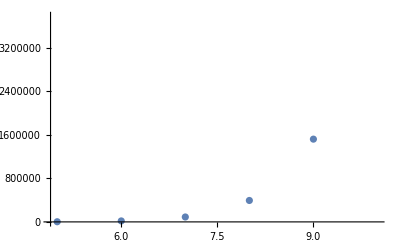

```mathematica
ListPlot[Transpose[{Table[i,{i,5,10}],cc}]]
```

```mathematica
bbb//N//MatrixForm
LUDecomposition[bbb][[-1]]
```

(0.0357933 | 0.883459 | 0.0756849 | 0. | 0. | 0. | 0. | 0.
0. | 0.0756849 | 0.81677 | 0.104925 | 0. | 0. | 0. | 0.
0. | 0. | 0.104925 | 0.766087 | 0.127309 | 0. | 0. | 0.
0. | 0. | 0. | 0.127309 | 0.726667 | 0.144865 | 0. | 0.
0. | 0. | 0. | 0. | 0.144865 | 0.695402 | 0.158898 | 0.
0. | 0. | 0. | 0. | 0. | 0.158898 | 0.670189 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.170293 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

1.5207020319558171704822313502458716537857973797053255775115935094189136695803251599912574043597×10^6

```mathematica
b=Table[r2[i,8,l,wgrid,wweights],{i,0,7}];
bb=b;bb[[;;,1]]=0;bb[[-1,;;]]=0;bb=Transpose[bb];
a=Table[divr2[i,8,l,wgrid,wweights],{i,0,7}];
(*aa=Inverse[a];*)
aa=PseudoInverse[Transpose[a]];
a//N//MatrixForm
LUDecomposition[a][[-1]]//N
Chop@aa//N//MatrixForm
LUDecomposition[a][[-1]]//N
bb//N//MatrixForm
LUDecomposition[b][[-1]]//N
LinearSolve[aa,tIn[[1;;5]]]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
27.9382 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-326.118 | 13.2127 | 0. | 0. | 0. | 0. | 0. | 0.
2518.46 | -102.852 | 9.53064 | 0. | 0. | 0. | 0. | 0.
-14886.1 | 608.025 | -57.3508 | 7.85488 | 0. | 0. | 0. | 0.
72457.8 | -2959.56 | 279.305 | -39.4013 | 6.90296 | 0. | 0. | 0.
-303534. | 12397.9 | -1170.07 | 165.275 | -30.2103 | 6.29336 | 0. | 0.
1.12695×10^6 | -46030.6 | 4344.2 | -613.677 | 112.452 | -24.7676 | 5.87223 | 0.)

LUDecomposition::sing: Matrix {{0,0,0,0,0,0,0,0},{«135»,«20»,«4»,«20»,0.},«5»,{1.126951242926390099025191811470025061303640093560007551530848564328159192466883798036633283×10^6,-46030.61285390541539928151951435177928670265371381865346734146483898669864795669998996419611,4344.197571275210248391755179451053121935440439318971146580305805404194091777297597366537225,-«136»,«136»,-«135»,5.872228533738763437036230437440563992403511166932659971440060979550638390967488078591874272,0.}} is singular.

∞

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0357933 | 0.883459 | 0.0756849 | 0. | 0. | 0. | 0. | 0.
0. | 0.0756849 | 0.81677 | 0.104925 | 0. | 0. | 0. | 0.
0. | 0. | 0.104925 | 0.766087 | 0.127309 | 0. | 0. | 0.
0. | 0. | 0. | 0.127309 | 0.726667 | 0.144865 | 0. | 0.
0. | 0. | 0. | 0. | 0.144865 | 0.695402 | 0.158898 | 0.
0. | 0. | 0. | 0. | 0. | 0.158898 | 0.670189 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.170293 | 0.)

LUDecomposition::sing: Matrix {{0,0,0,0,0,0,0,0},{«135»,«20»,«4»,«20»,0.},«5»,{1.126951242926390099025191811470025061303640093560007551530848564328159192466883798036633283×10^6,-46030.61285390541539928151951435177928670265371381865346734146483898669864795669998996419611,4344.197571275210248391755179451053121935440439318971146580305805404194091777297597366537225,-«136»,«136»,-«135»,5.872228533738763437036230437440563992403511166932659971440060979550638390967488078591874272,0.}} is singular.

∞

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0357933 | 0.883459 | 0.0756849 | 0. | 0. | 0. | 0. | 0.
0. | 0.0756849 | 0.81677 | 0.104925 | 0. | 0. | 0. | 0.
0. | 0. | 0.104925 | 0.766087 | 0.127309 | 0. | 0. | 0.
0. | 0. | 0. | 0.127309 | 0.726667 | 0.144865 | 0. | 0.
0. | 0. | 0. | 0. | 0.144865 | 0.695402 | 0.158898 | 0.
0. | 0. | 0. | 0. | 0. | 0.158898 | 0.670189 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.170293 | 0.)

2.67892

LinearSolve::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

LinearSolve[{{0,0,0,0,0,0,0,0},{0.03579334344404064038165772992646681092893093542188885613800352101064308876392146803209406627,0.8834586466165413533834586466165413533834586466165413533834586466165413533834586466165413534,0.0756848754445530808964758815092203900788525546468559411094109643403445709883305853083808364,0.,0.,0.,0.,0},{0.,0.0756848754445530808964758815092203900788525546468559411094109643403445709883305853083808364,0.8167701863354037267080745341614906832298136645962732919254658385093167701863354037267080745,0.104924706430806824613505750717565127110118964356629467409127135163081007570839728630032421,0.,0.,0.,0},{0.,0.,0.104924706430806824613505750717565127110118964356629467409127135163081007570839728630032421,0.7660869565217391304347826086956521739130434782608695652173913043478260869565217391304347826,0.127309435265781882629781850706749158988557563201353184464758279621244856534154254916836769,0.,0.,0},{0.,0.,0.,0.127309435265781882629781850706749158988557563201353184464758279621244856534154254916836769,0.7266666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,0.144865311534399034538032470626378127688095483145513987792017655060229914297681512592327283,0.,0},{0.,0.,0.,0.,0.144865311534399034538032470626378127688095483145513987792017655060229914297681512592327283,0.6954022988505747126436781609195402298850574712643678160919540229885057471264367816091954023,0.158897541646478525504326330330732196278172632088415690498682710352875498680675372224592088,0},{0.,0.,0.,0.,0.,0.158897541646478525504326330330732196278172632088415690498682710352875498680675372224592088,0.6701890989988876529477196885428253615127919911012235817575083426028921023359288097886540601,0},{0.,0.,0.,0.,0.,0.,0.1702930998435298267803365733646427864342303348943335770854008318666512525060095560772708596,0}},{139.1560052360896574984089971507672029478136836219211113213232446699532985060254682377085020352611,69.0756666040470503497148873786102739879717617499613260246285831933181639250648847894343107608804,22.,0.,0}]

```mathematica
divrdrClean[f_,l_,t_]:=Module[{out,bad},
out = Simplify[1/t D[t f,t]];
bad=Coefficient[out,t,l-2];
out=out-bad t^(l-2);
out]
```